-Graphics-

(Bienvenidos a mmAeScience!
https://github.com/josemramirez/mmaescience -[for MMaTeX])_beta^v14

# eScience - Trabajar con Límites (1)

◀ prev - + prox ▶

e Guardar
d Resetear

### Visión general

```mathematica
Las funciones cubiertas hasta ahora calculan las cantidades deseadas, dada alguna entrada.
```

```mathematica
Aquí está el gráfico de la función f[x]=x:
```

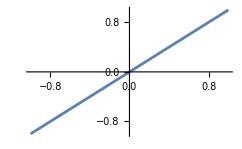

```mathematica
Plot[x, {x, -1, 1}]
```

Mejorado:

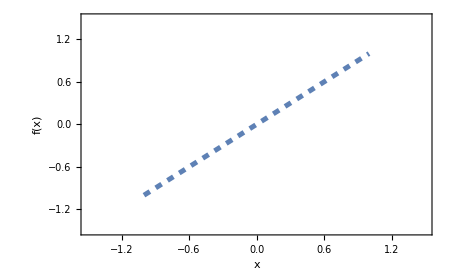

```mathematica
Plot[x, {x, -1, 1}, PlotLegends -> "Expressions",Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,19],
PlotRange->{{-1.5,1.5},{-1.5,1.5}},
PlotStyle->{
{Thickness@0.008,Dashed}},
FrameLabel->{Style["x",24],Style["f(x)",24]},
ImageSize->450]
```

Sin embargo, a veces las funciones no están definidas en ciertos puntos, aunque parezca que lo están en sus gráficas.

```mathematica
Aquí está la gráfica de la función g[x]=x^2/x:
```

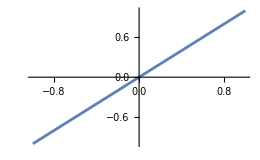

```mathematica
Plot[x^2/x, {x, -1, 1}]
```

Se parece al gráfico anterior, pero no está definido en 0:

```mathematica
g[x_] :=x^2/x
```

```mathematica
Quiet[g[0]]
```

Indeterminate

```mathematica
Aunque no esté definido allí, es posible que desee conocer el comportamiento de la función cerca del punto. Esta lección explorará esta noción matemáticamente con el concepto conocido como límite.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Noción de límite

Los límites surgen naturalmente en muchas áreas de las matemáticas aplicadas y teóricas. Para encontrar un límite, se ve a qué se aproxima la función cuando x se acerca a un determinado valor.

Por ejemplo, considere la siguiente función:

```mathematica
f[x_] := x^2  - x + 2
```

Las siguientes tablas proporcionan valores de f para valores de x que se acercan cada vez más a 1 (¡pero sin incluir 1!):

{x | x^2-x+2
0 | 2.
0.5 | 1.75
0.9 | 1.91
0.95 | 1.9525
0.99 | 1.9901
0.995 | 1.99503
0.999 | 1.999,x | x^2-x+2
2 | 4.
1.5 | 2.75
1.1 | 2.11
1.05 | 2.0525
1.01 | 2.0101
1.005 | 2.00503
1.001 | 2.001}

Parece que los valores de la función se acercan cada vez más a 2 a medida que los valores se acercan cada vez más a 1 desde cualquier lado.

Aquí hay un gráfico que hace lo mismo.

◀ prev - + prox ▶

e Guardar
d Resetear

### Función racional trigonométrica

```mathematica
Calcule el siguiente límite a medida que x tiende a 0:
```

```mathematica
f[x_] := Sin[x]/x
```

```mathematica
Haz una tabla de valores para la función:
```

{x | (sin(x))/x
-1 | 0.841471
-0.5 | 0.958851
-0.1 | 0.998334
-0.05 | 0.999583
-0.01 | 0.999983
-0.005 | 0.999996
-0.001 | 1.,x | (sin(x))/x
1 | 0.841471
0.5 | 0.958851
0.1 | 0.998334
0.05 | 0.999583
0.01 | 0.999983
0.005 | 0.999996
0.001 | 1.}

A continuación se muestra un gráfico de la función:

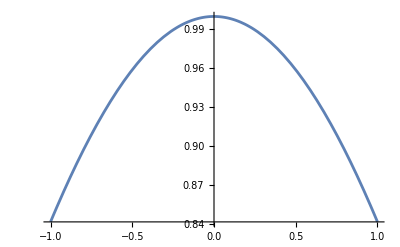

```mathematica
Plot[f[x], {x, -1, 1}]
```

Está claro que la función se aproxima a 1 cuando x tiende a 0.

```mathematica
Con Límite, puede calcular el límite de cualquier función en cualquier momento. El límite anterior es:
```

```mathematica
Limit[f[x], x -> 0]
```

1

◀ prev - + prox ▶

e Guardar
d Resetear

### Función racional con una discontinuidad removible

Calcule el siguiente límite a medida que x tiende a −1:

```mathematica
f[x_] :=(x + 1)/ (x^2  - 1)
```

```mathematica
Comience haciendo una tabla de valores para la función:
```

{x | (x+1)/(x^2-1)
-2 | -0.333333
-1.5 | -0.4
-1.1 | -0.47619
-1.05 | -0.487805
-1.01 | -0.497512
-1.005 | -0.498753
-1.001 | -0.49975,x | (x+1)/(x^2-1)
0 | -1.
-0.5 | -0.666667
-0.9 | -0.526316
-0.95 | -0.512821
-0.99 | -0.502513
-0.995 | -0.501253
-0.999 | -0.50025}

A continuación se muestra un gráfico de la función:

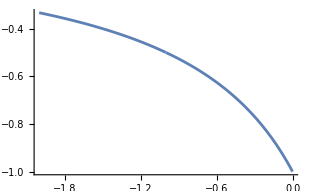

```mathematica
Plot[f[x], {x, -2, 0}, GridLines -> {{-1}, {-1/2}}]
```

Las líneas de cuadrícula se agregan con GridLines para ayudar a ver el valor de la función. Está claro que la función se aproxima a −0,5 cuando x tiende a −2.

Puedes confirmar esta respuesta usando Límite:

```mathematica
Limit[f[x], x -> -1]
```

-1/2

◀ prev - + prox ▶

e Guardar
d Resetear

### Función a trozos

```mathematica
Calcule el siguiente límite a medida que x tiende a −1:
```

```mathematica
g[x_] := Piecewise[{{-0.75, x == -1}}, (x + 1)/(  x^2  - 1)]
```

```mathematica
Comience haciendo una tabla de valores para la función:
```

{x | (x+1)/(x^2-1)
-2 | -0.333333
-1.5 | -0.4
-1.1 | -0.47619
-1.05 | -0.487805
-1.01 | -0.497512
-1.005 | -0.498753
-1.001 | -0.49975,x | (x+1)/(x^2-1)
0 | -1.
-0.5 | -0.666667
-0.9 | -0.526316
-0.95 | -0.512821
-0.99 | -0.502513
-0.995 | -0.501253
-0.999 | -0.50025}

A continuación se muestra un gráfico de la función:

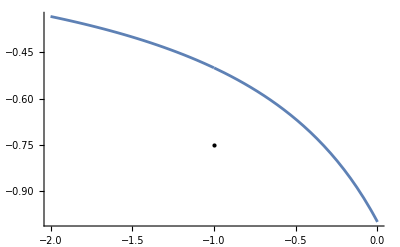

```mathematica
Plot[g[x], {x, -2, 0}, GridLines -> {{-1}, {-1/2}}, Epilog -> {PointSize[Large], Point[{-1, g[-1]}]}]
```

```mathematica
La función sigue siendo cercana a −0.5 a medida que x se aproxima a −1.
```

Puedes confirmar esta respuesta usando Límite:

```mathematica
Limit[g[x], x -> 0]
```

-1

◀ prev - + prox ▶

e Guardar
d Resetear

### Función algebraica con discontinuidad removible

```mathematica
Calcule el siguiente límite a medida que x tiende a 0:
```

```mathematica
f[x_] :=Sqrt[x^2  + 4] - 2/x^2
```

Comience haciendo una tabla de valores para la función:

{x | (√(x^2+4)-2)/x^2
-2 | 0.207107
-1.5 | 0.222222
-1.1 | 0.233506
-1.05 | 0.234804
-1.01 | 0.235818
-1.005 | 0.235943
-1.001 | 0.236043,x | (√(x^2+4)-2)/x^2
0 | Indeterminate
-0.5 | 0.246211
-0.9 | 0.238483
-0.95 | 0.237295
-0.99 | 0.236316
-0.995 | 0.236192
-0.999 | 0.236093}

```mathematica
A continuación se muestra un gráfico de la función:
```

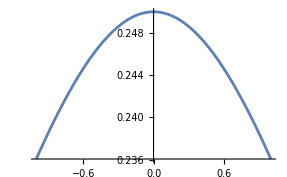

```mathematica
Plot[f[x], {x, -1, 1}]
```

Está claro que la función se aproxima a 0,25 cuando x se aproxima a 0.

Puedes confirmar esta respuesta usando Límite:

```mathematica
Limit[f[x], x -> 0]
```

1/4

◀ prev - + prox ▶

e Guardar
d Resetear

### Función trigonométrica

```mathematica
Calcule el siguiente límite a medida que x tiende a 0:
```

```mathematica
f[x_] := Cos[π/x]
```

```mathematica
Comience haciendo una tabla de valores para la función:
```

{x | cos(π/x)
-1 | -1.
-0.5 | 1.
-0.1 | 1.
-0.05 | 1.
-0.01 | 1.
-0.005 | 1.
-0.001 | 1.,x | cos(π/x)
1 | -1.
0.5 | 1.
0.1 | 1.
0.05 | 1.
0.01 | 1.
0.005 | 1.
0.001 | 1.}

Parece que la función se aproxima a 1 cuando x se aproxima a 0, pero es mucho más complicado de lo que parece.

Aquí hay un ejemplo interactivo para ilustrar.

```mathematica
La función no parece acercarse a ningún valor en particular cuando x tiende a 0, como se muestra en Limit:
```

```mathematica
Limit[f[x], x -> 0]
```

Indeterminate

◀ prev - + prox ▶

e Guardar
d Resetear

### Suma de funciones trigonométricas y polinómicas

Calcule el siguiente límite a medida que x tiende a 0:

```mathematica
f[x_] := 4 x^5  + 3 Cos[100 x]/200
```

Comience haciendo una tabla de valores para la función:

{x | 4 x^5+3/200 cos(100 x)
-1 | -3.98707
-0.5 | -0.110526
-0.1 | -0.0126261
-0.05 | 0.00425368
-0.01 | 0.00810453
-0.005 | 0.0131637
-0.001 | 0.0149251,x | 4 x^5+3/200 cos(100 x)
1 | 4.01293
0.5 | 0.139474
0.1 | -0.0125461
0.05 | 0.00425618
0.01 | 0.00810453
0.005 | 0.0131637
0.001 | 0.0149251}

```mathematica
Parece que la función se aproxima a 3/200 (0,015) cuando x se aproxima a 0.
```

```mathematica
A continuación se muestra un gráfico de la función:
```

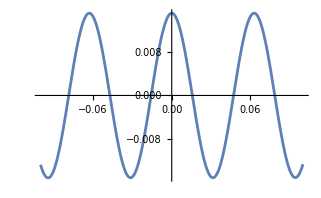

```mathematica
Plot[f[x], {x, -0.1, 0.1}, PlotRange -> All]
```

```mathematica
Puedes confirmar esta respuesta usando Límite:
```

```mathematica
Limit[f[x], x -> 0]
```

3/200

◀ prev - + prox ▶

e Guardar
d Resetear

### Límites unilaterales

```mathematica
El límite de la izquierda es el valor al que se aproxima una función a medida que avanza desde la izquierda.
```

El límite de la derecha es el valor al que se aproxima una función a medida que avanza desde la derecha.

El límite de una función existe si el límite de la izquierda y el límite de la derecha son iguales.

```mathematica
Calcule el siguiente límite a medida que x tiende a 0:
```

```mathematica
f[x_] := Piecewise[{{-1, x < 0}}, 1]
```

Dada la naturaleza de f, no es necesaria una tabla. Aquí hay un gráfico de f en su lugar:

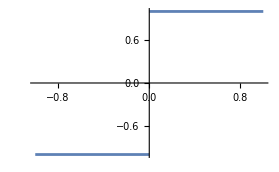

```mathematica
Plot[f[x], {x, -1, 1}]
```

Está claro que el límite de la izquierda en 0 es −1, y el límite de la derecha en 0 es 1.

```mathematica
Confirme esta respuesta usando Límite y la opción Dirección. "DesdeDeAbajo" significa un límite a la izquierda. "DesdeArriba" significa un límite a la derecha:
```

```mathematica
{Limit[f[x], x -> 0, Direction -> "FromBelow"], Limit[f[x], x -> 0, Direction -> "FromAbove"]}
```

{-1,1}

Por lo tanto, el límite no existe:

```mathematica
Limit[f[x], x -> 0]
```

Indeterminate

◀ prev - + prox ▶

e Guardar
d Resetear

### Función general a trozos

```mathematica
Calcule el límite de la siguiente función cuando x tiende a 1, 4 y 6:
```

```mathematica
f[x_] := Piecewise[{{4, x == 1}, {3 Cos[x - 1], x < 1}, {3 Sqrt[x], x > 1 && x < 6}}, 3 x - 13]
```

Comience trazando la función:

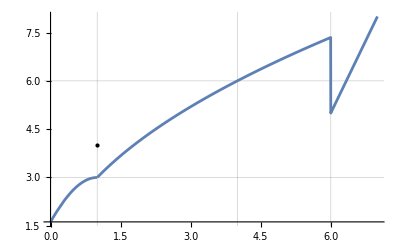

```mathematica
Plot[f[x], {x, 0, 7}, GridLines -> {{1, 4, 6}, {3, 6}}, Epilog -> {PointSize[Large], Point[{1, f[1]}]}]
```

```mathematica
Está claro que la función se aproxima a 3 cuando x se aproxima a 1, se aproxima a 6 para x=4, y no existe para x=6.
```

```mathematica
Confirme esta respuesta usando Límite:
```

```mathematica
(Limit[f[x], x -> #1] & ) /@ {1, 4, 6}
```

{3,6,Indeterminate}

```mathematica
Puede utilizar los símbolos #, & y /@ para encontrar el límite de cada uno de los valores de la lista.
```

De nuevo, el límite no existe en 6, ya que los límites de la izquierda y de la derecha en 6 son diferentes:

```mathematica
{Limit[f[x], x -> 6, Direction -> "FromBelow"], Limit[f[x], x -> 6, Direction -> "FromAbove"]}
```

{3 √6,5}

◀ prev - + prox ▶

e Guardar
d Resetear

### Tabla de valores

```mathematica
Calcule el límite de la siguiente función cuando x tiende a −1, dados los valores x=−2, −1.5, −1.1, −1.01, −1.001, −0.999, −0.99, −0.95, −0.9, −0.5 y 0.
```

```mathematica
f[x_] := (x^2  + 2 x)/(x^2  - 4 x - 5)
```

```mathematica
Haga un gráfico para la función usando Cuadrícula, Unión y Tabla:
```

x | (2 x+x^2)/(-5-4 x+x^2)
-2 | 0
-1.5 | -0.230769
-1.1 | -1.62295
-1.01 | -16.6373
-1.001 | -166.639
-0.999 | 166.694
-0.99 | 16.6928
-0.95 | 3.35294
-0.9 | 1.67797
-0.5 | 0.272727
0 | 0

```mathematica
Parece que la función se aproxima a ∞ desde la izquierda y a −∞ desde la derecha cuando x se aproxima a −1. Por lo tanto, el límite no debería existir.
```

```mathematica
Confirmar con límite:
```

```mathematica
{Limit[f[x], x -> -1, Direction -> "FromBelow"], Limit[f[x], x -> -1, Direction -> "FromAbove"]}
```

{-∞,∞}

```mathematica
Limit[f[x], x -> -1]
```

Indeterminate

◀ prev - + prox ▶

e Guardar
d Resetear

### Asíntota vertical 1

Calcule el siguiente límite cuando x tiende a 1:

```mathematica
f[x_] :=1/(x - 1)^2
```

```mathematica
Comience haciendo una tabla de valores para la función:
```

{x | 1/(x-1)^2
0 | 1.
0.5 | 4.
0.9 | 100.
0.95 | 400.
0.99 | 10000.
0.995 | 40000.
0.999 | 1.×10^6,x | 1/(x-1)^2
2 | 1.
1.5 | 4.
1.1 | 100.
1.05 | 400.
1.01 | 10000.
1.005 | 40000.
1.001 | 1.×10^6}

A continuación se muestra un gráfico de la función:

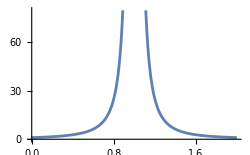

```mathematica
Plot[f[x], {x, 0, 2}]
```

Está claro que la función se aproxima a ∞ desde ambos lados cuando x tiende a 1.

Confirmar con límite:

```mathematica
Limit[f[x], x -> 1]
```

∞

◀ prev - + prox ▶

e Guardar
d Resetear

### Asíntota vertical 2

```mathematica
Calcule el siguiente límite a medida que x tiende a 0:
```

```mathematica
f[x_] :=1/x
```

Comience haciendo una tabla de valores para la función:

{x | 1/x
-1 | -1.
-0.5 | -2.
-0.1 | -10.
-0.05 | -20.
-0.01 | -100.
-0.005 | -200.
-0.001 | -1000.,x | 1/x
1 | 1.
0.5 | 2.
0.1 | 10.
0.05 | 20.
0.01 | 100.
0.005 | 200.
0.001 | 1000.}

```mathematica
Añade un gráfico para que quede más claro:
```

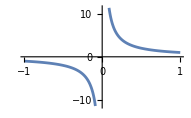

```mathematica
Plot[f[x], {x, -1, 1}]
```

Está claro que la función se aproxima a −∞ desde la izquierda y ∞ desde la derecha cuando x tiende a 0; por lo tanto, el límite no existe.

```mathematica
Confirmar con límite:
```

```mathematica
{Limit[f[x], x -> 0, Direction -> "FromBelow"], Limit[f[x], x -> 0, Direction -> "FromAbove"]}
```

{-∞,∞}

```mathematica
Limit[f[x], x -> 0]
```

Indeterminate

◀ prev - + prox ▶

e Guardar
d Resetear

### Hallar las asíntotas de una función

Halla las asíntotas de la siguiente función en el rango de −2π a 2π:

```mathematica
f[x_] := Cot[x]
```

Comience trazando la función:

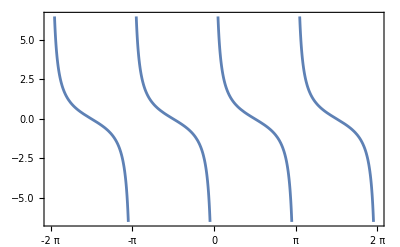

```mathematica
Plot[f[x], {x, -2 Pi, 2 Pi}, Frame -> True, FrameTicks -> {{Automatic, None}, {{-2 Pi, -Pi, 0, Pi, 2 Pi}, None}}]
```

La función se aproxima a −∞ desde la izquierda y ∞ desde la derecha cuando x se aproxima a múltiplos enteros de π:

```mathematica
list = Table[n Pi, {n, -2, 2}]
```

{-2 π,-π,0,π,2 π}

Limit muestra que los límites izquierdo y derecho no son los mismos en 0:

```mathematica
{Limit[f[x], x -> 0, Direction -> "FromBelow"], Limit[f[x], x -> 0, Direction -> "FromAbove"]}
```

{-∞,∞}

Para todos los múltiplos enteros de π, el límite no existe:

```mathematica
Limit[f[x], x -> list]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

◀ prev - + prox ▶

e Guardar
d Resetear

### Cociente de diferencia y tabla de valores

Calcule el límite de la siguiente función cuando h tiende a 0:

```mathematica
f[h_] := (x + h)^2  - x^2/h
```

Graficar esto no te llevará a ninguna parte, así que haz una tabla de valores para h a la izquierda y a la derecha de 0:

-1 | -1+2 x
-0.5 | -0.5+2. x
-0.1 | -0.1+2. x
-0.01 | -0.01+2. x
-0.001 | -0.001+2. x
0.001 | 0.001+2. x
0.01 | 0.01+2. x
0.05 | 0.05+2. x
0.1 | 0.1+2. x
0.5 | 0.5+2. x
1 | 1+2 x

Está claro que la función se aproxima a 2x cuando h se aproxima a 0.

```mathematica
Confirmar con límite:
```

```mathematica
Limit[f[h], h -> 0]
```

2 x

◀ prev - + prox ▶

e Guardar
d Resetear

### Resumen

```mathematica
Los límites dan el valor de la función a la que se aproxima una función a medida que su entrada se acerca a algún valor.
```

No es necesario definir la función en el valor para tener un límite allí.

```mathematica
Siempre que el límite de la derecha y el límite de la izquierda sean iguales en un punto, el límite existe en el punto.
```

```mathematica
Las tablas son útiles para encontrar límites.
```

```mathematica
La siguiente lección cubrirá las leyes de límites, que dan formas de calcular límites sin usar tablas.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 1: Función racional

```mathematica
Calcule el límite de la siguiente función cuando x tiende a 1:
```

```mathematica
f[x_] := (x^5  - 1)/(x-1)
```

#### Solución

```mathematica
Comience haciendo una tabla de valores para la función:
```

{x | (x^5-1)/(x^10-1)
0 | 1.
0.5 | 0.969697
0.9 | 0.628737
0.95 | 0.563767
0.99 | 0.51256
0.995 | 0.506265
0.999 | 0.501251,x | (x^5-1)/(x^10-1)
2 | 0.030303
1.5 | 0.116364
1.1 | 0.383067
1.05 | 0.439313
1.01 | 0.487565
1.005 | 0.493766
1.001 | 0.498751}

```mathematica
A continuación se muestra un gráfico de la función:
```

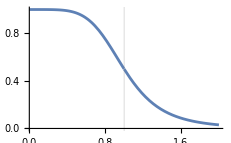

```mathematica
Plot[f[x], {x, 0, 2}, GridLines -> {{1}, None}]
```

Está claro que la función se aproxima a 0,5 cuando x se aproxima a 1.

Confirmar con límite:

```mathematica
Limit[f[x], x -> 1]
```

1/2

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 2: Función trigonométrica dada una tabla de valores

Calcule el límite para la siguiente función cuando x tiende a 0, dados los valores x=-1, −0.5, −0.1, −0.01, −0.001, 0.001, 0.01, 0.05, 0.1, 0.5 y 1.

```mathematica
f[x_] :=  Sin[x]/(x - Tan[x])
```

#### Solución

```mathematica
Haz un gráfico para la función:
```

-1. | -1.50961
-0.5 | -10.3542
-0.1 | -298.302
-0.01 | -29998.3
-0.001 | -3.×10^6
0.001 | -3.×10^6
0.01 | -29998.3
0.05 | -1198.3
0.1 | -298.302
0.5 | -10.3542
1. | -1.50961

Parece que la función se aproxima a −∞ desde la izquierda y la derecha a medida que x se acerca a 0. Por lo tanto, el límite debe ser −∞.

```mathematica
Confirmar con límite:
```

```mathematica
Limit[f[x], x -> 0]
```

-∞

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 3: Cociente diferencial

```mathematica
Calcule el límite de la siguiente función cuando h tiende a 0:
```

```mathematica
f[h_] := ((2 + h)^5  - 32)/h
```

#### Solución

```mathematica
Comience haciendo una tabla de valores para la función:
```

{x | ((x+2)^5-32)/x
-1 | 31.
-0.5 | 48.8125
-0.1 | 72.3901
-0.05 | 76.0988
-0.01 | 79.204
-0.005 | 79.601
-0.001 | 79.92,x | ((x+2)^5-32)/x
1 | 211.
0.5 | 131.313
0.1 | 88.4101
0.05 | 84.1013
0.01 | 80.804
0.005 | 80.401
0.001 | 80.08}

A continuación se muestra un gráfico de la función:

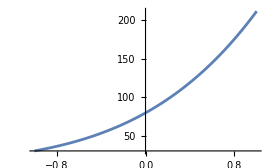

```mathematica
Plot[f[h], {h, -1, 1}]
```

Parece que la función se aproxima a 80 cuando h se acerca a 0.

Confirmar con límite:

```mathematica
Limit[f[h], h -> 0]
```

80

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 4: ¿Dónde no existe el límite?

Encuentre los lugares donde no existe el límite para la siguiente función:

```mathematica
f[x_] := Piecewise[{{1 + x, x < -1}, {2 x^2 , -1 <= x <= 1}}, 3 - x]
```

#### Solución

```mathematica
Grafique la función:
```

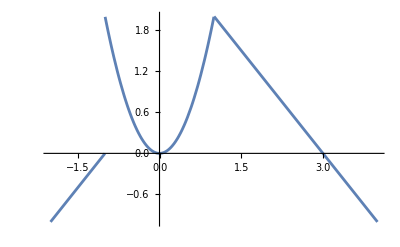

```mathematica
Plot[f[x], {x, -2, 4}]
```

Parece que el límite no existe en −1.

```mathematica
Confirmar con límite:
```

```mathematica
{Limit[f[x], x -> -1, Direction -> "FromBelow"], Limit[f[x], x -> -1, Direction -> "FromAbove"]}
```

{0,2}

```mathematica
En x=1, el límite también existe aunque no sea suave allí:
```

```mathematica
{Limit[f[x], x -> 1, Direction -> "FromBelow"], Limit[f[x], x -> 1, Direction -> "FromAbove"]}
```

{2,2}

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 5: Una aplicación de la relatividad especial

```mathematica
La teoría de la relatividad especial fue desarrollada por Albert Einstein.
```

En relatividad especial, la masa de una partícula con masa en reposo Subíndice[m, 0] y velocidad v viene dada por la siguiente función:

```mathematica
mass[v_] :=m0/Sqrt[1- v^2 /c^2]
```

```mathematica
c = 299792458;
```

```mathematica
m0 = 1;
```

```mathematica
Aquí c es la velocidad de la luz en el vacío. Sea la masa restante 1.
```

```mathematica
¿Cuál es el límite de la masa cuando v tiende a c?
```

#### Solución

```mathematica
Vea lo que sucede cuando v se acerca a c desde la izquierda:
```

2.99792×10^8 | 12243.2
2.99792×10^8 | 17314.5
2.99792×10^8 | 38716.4
2.99792×10^8 | 122432.
2.99792×10^8 | 387169.

Debido al tamaño de c, hay algún error, pero en general parece acercarse a ∞ desde la izquierda.

```mathematica
Confirmar con límite:
```

```mathematica
Limit[mass[v], v -> c, Direction -> "FromBelow", Assumptions -> m0 > 0 && c > 0]
```

∞

```mathematica
mmAeScienceDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mmAeScienceDB/"<>mmAeScienceDB1,"Global`"];
```

```mathematica
buttons=Row[{
Column[{
Button["e Guardar",(NotebookFind[EvaluationNotebook[],#,All,CellTags];SelectionEvaluate[EvaluationNotebook[]])&/@{"mmAeSRunSave"};],
Button["d Resetear",(NotebookFind[EvaluationNotebook[],#,All,CellTags];SelectionEvaluate[EvaluationNotebook[]])&/@{"mmAeSRunCollapse"};]
}]
}]
```

e Guardar
d Resetear